# Parametric Amplified Quantum Transducer

This notebook is for the paper Parametric Amplification of an Optomechanical Quantum Interconnect, now on arXiv:2202.12291.

## Definitions

```mathematica
<<(NotebookDirectory[]<>"Transducer.wl");
```

First we define the symbols and assumptions used in this notebook.

```mathematica
<<Notation`
Symbolize[Subscript[a, _]];Symbolize[Subscript[a, _]^†];Symbolize[Subscript[Δ, _]];Symbolize[Subscript[ω, _]];Symbolize[Subscript[κ, _]];Symbolize[Subscript[G, e]];Symbolize[Subscript[G, o]];Symbolize[Subscript[g, o]];Symbolize[Subscript[g, e]];
AssumptionRealValues={Subscript[Ω, o]∈Reals,Subscript[Ω, e]∈Reals,Ω∈Reals,Subscript[ω, m]∈Reals,t∈Reals,Subscript[κ, o]∈Reals,Subscript[κ, e]∈Reals,κ∈Reals,Subscript[Δ, e]∈Reals,Subscript[Δ, o]∈Reals,Δ∈Reals,Subscript[g, e]∈Reals,Subscript[g, o]∈Reals};
```

Next, we define the symbolic linear system.

```mathematica
(*The A(t) matrix*)
Amat={{-ⅈ*Subscript[Δ, o]-Subscript[κ, o]/2,0,-ⅈ*Subscript[G, o],0,0,-ⅈ*Subscript[G, o]},{0,-ⅈ*Subscript[Δ, e]-Subscript[κ, e]/2,-ⅈ*Subscript[G, e],0,0,-ⅈ*Subscript[G, e]},{-ⅈ*Conjugate[Subscript[G, o]],-ⅈ*Conjugate[Subscript[G, e]],-ⅈ*Subscript[ω, m]-Subscript[κ, m]/2,-ⅈ*Subscript[G, o],-ⅈ*Subscript[G, e],0},{0,0,ⅈ*Conjugate[Subscript[G, o]],ⅈ*Subscript[Δ, o]-Subscript[κ, o]/2,0,ⅈ*Conjugate[Subscript[G, o]]},{0,0,ⅈ*Conjugate[Subscript[G, e]],0,ⅈ*Subscript[Δ, e]-Subscript[κ, e]/2,ⅈ*Conjugate[Subscript[G, e]]},{ⅈ*Conjugate[Subscript[G, o]], ⅈ*Conjugate[Subscript[G, e]],0,ⅈ*Subscript[G, o],ⅈ*Subscript[G, e],ⅈ*Subscript[ω, m]-Subscript[κ, m]/2}};
(*The B matrix*)
Bmat=DiagonalMatrix[{Sqrt[Subscript[κ, o,ex]],Sqrt[Subscript[κ, e,ex]],Sqrt[Subscript[κ, m,ex]],Sqrt[Subscript[κ, o,ex]],Sqrt[Subscript[κ, e,ex]],Sqrt[Subscript[κ, m,ex]]}];
(*The κ matrix*)
Kmat=DiagonalMatrix[{Subscript[κ, o],Subscript[κ, e],Subscript[κ, m],Subscript[κ, o],Subscript[κ, e],Subscript[κ, m]}];
(*State vector*)
Av[t_]:={Subscript[a, o][t],Subscript[a, e][t],Subscript[a, m][t],SuperDagger[Subscript[a, o]][t],SuperDagger[Subscript[a, e]][t],SuperDagger[Subscript[a, m]][t]};
(*Input vector*)
Ain[t_]:={0,-1/(√(2*π))*Exp[-ⅈ*Subscript[ω, m]*t],0,0,-1/(√(2*π))*Exp[ⅈ*Subscript[ω, m]*t],0};
```

We split the A (t) matrix into three parts

```mathematica
ADcompMap=AmatDecompose[Amat];
Ad="diag"/.ADcompMap;
Am="G"/.ADcompMap;
Ap="G^*"/.ADcompMap;
```

### Functions

In the following cell, we define useful functions for later sections.

```mathematica
SolveTransferOsc[Ad_,Ap_,Am_,N_,ω_,ωm_]:=Module[{Ξ,iden},
iden=IdentityMatrix[Dimensions[Ad,1][[1]]];
Ξ=IterativeΞ[Ad,Ap,Am,N,ω,ωm];
Inverse[Bmat].Kmat.Inverse[-ⅈ*ω*iden-Ad-Ξ[[1]]-Ξ[[2]]].Bmat-iden//Simplify
]
SolveTransducerConstDrive[NumericRules_,tf_]:=Module[{GRule,AmatN,eqns},
GRule={Subscript[G, e]->SolveODEConst[Subscript[Δ, e],Subscript[κ, e],Subscript[Ω, e],t]*Subscript[g, e]/.{NumericRules}[[1]],Subscript[G, o]->SolveODEConst[Subscript[Δ, o],Subscript[κ, o],Subscript[Ω, o],t]*Subscript[g, o]/.{NumericRules}[[1]]};
AmatN=Amat/.GRule;
eqns=Join[Thread[D[Av[t],t]==AmatN.Av[t]+Bmat.Ain[t]],Thread[Av[0]==0]]/.NumericRules//Simplify;
NDSolve[eqns,{Subscript[a, o],Subscript[a, e],Subscript[a, m],SuperDagger[Subscript[a, o]],SuperDagger[Subscript[a, e]],SuperDagger[Subscript[a, m]]},{t,0,tf}]
]
SolveTransducerOscDrive[NumericRules_,tf_]:=Module[{GRule,AmatN,eqns},
GRule={Subscript[G, e]->SolveODEOsc[Subscript[Δ, e],Subscript[κ, e],Subscript[Ω, e],2*Subscript[ω, m],t]*Subscript[g, e]/.{NumericRules}[[1]],Subscript[G, o]->SolveODEOsc[Subscript[Δ, o],Subscript[κ, o],Subscript[Ω, o],2*Subscript[ω, m],t]*Subscript[g, o]/.{NumericRules}[[1]]};
AmatN=Amat/.GRule;
eqns=Join[Thread[D[Av[t],t]==AmatN.Av[t]+Bmat.Ain[t]],Thread[Av[0]==0]]/.NumericRules//Simplify;
NDSolve[eqns,{Subscript[a, o],Subscript[a, e],Subscript[a, m],SuperDagger[Subscript[a, o]],SuperDagger[Subscript[a, e]],SuperDagger[Subscript[a, m]]},{t,0,tf}]
]
```

### Numerical value

Finally, we define all the numerical values used in the simulation.

```mathematica
HigginPaper={Subscript[κ, e]->2.5*2*π,Subscript[κ, e,ex]->2.3*2*π,Subscript[Δ, e]->1.47*2*π,Subscript[g, e]->3.8*2*π*10^-6,Subscript[κ, o]->2.1*2*π,Subscript[κ, o,ex]->1.1*2*π,Subscript[Δ, o]->1.11*2*π,Subscript[g, o]->6.6*2*π*10^-6,Subscript[κ, m]->N[11*2*π*10^-6],Subscript[κ, m,ex]->2*π*10^-6,Subscript[ω, m]->1.4732*2*π,Subscript[Ω, e]->2*π*500,Subscript[Ω, o]->2*π*500};
SymValues={κ->2.5*2*π,Subscript[κ, e,ex]->2.3*2*π,g->3.8*2*π*10^-6,Subscript[κ, o,ex]->1.1*2*π,Subscript[ω, m]->1.4732*2*π,Ω->2*π*500};
```

## ODE solution to the intra-cavity photon number

### Constant control

The full solution is:

```mathematica
SolveODEConst[Δ,κ,Ω,t]
```

(2 (-1+ⅇ^(-1/2 t (2 ⅈ Δ+κ))) Ω)/(2 Δ-ⅈ κ)

The steady state solution is:

```mathematica
SolveSteadyConst[Δ,κ,Ω]
```

-(2 Ω)/(2 Δ-ⅈ κ)

```mathematica
SolveSteadyConst[Δ,κ,Ω]
```

-(2 Ω)/(2 Δ-ⅈ κ)

### Oscillating control

The full solution is:

```mathematica
SolveODEOsc[Δ,κ,Ω,2*Subscript[ω, m],t]
```

(2 (ⅇ^(-ⅈ t Δ-(t κ)/2)-ⅇ^(-2 ⅈ t ω_m)) Ω)/(2 Δ-ⅈ κ-4 ω_m)

The amplitude of steady state solution is:

```mathematica
SolveSteadyOsc[Δ,κ,Ω,2*Subscript[ω, m]]
```

-(2 Ω)/(2 Δ-ⅈ κ-4 ω_m)

### Plotting α values

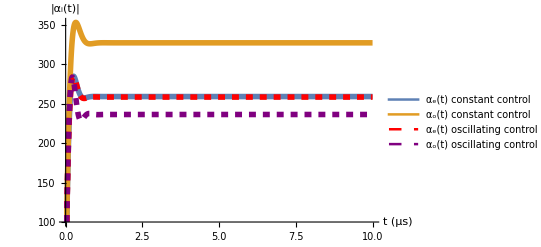

```mathematica
fy=Join[{Abs[SolveODEConst[Subscript[Δ, e],Subscript[κ, e],Subscript[Ω, e],t]]/.HigginPaper,Abs[SolveODEConst[Subscript[Δ, o],Subscript[κ, o],Subscript[Ω, o],t]]/.HigginPaper},{Abs[SolveODEOsc[Subscript[Δ, e],Subscript[κ, e],Subscript[Ω, e],2*Subscript[ω, m],t]]/.HigginPaper,Abs[SolveODEOsc[Subscript[Δ, o],Subscript[κ, o],Subscript[Ω, o],2*Subscript[ω, m],t]]/.HigginPaper}];
p=Plot[fy,{t,0,10},PlotStyle->{{Line,Thickness[0.01]},{Line,Thickness[0.01]},{Red,Dashed,Thickness[0.01]},{Purple,Dashed,Thickness[0.01]}},BaseStyle->{FontFamily->"Times New Roman",15},LabelStyle->{FontFamily->"Times New Roman",15},AxesLabel->{"t (μs)","|α_i(t)|"},PlotLegends->Placed[{Row[{Subscript["α","e"],"(t) constant control"}],Row[{Subscript["α","o"],"(t) constant control"}],Row[{Subscript["α","e"],"(t) oscillating control"}],Row[{Subscript["α","o"],"(t) oscillating control"}]},Right]]
```

## Case study

### Constant drive

#### Sanity check

The steady state A (t) matrix is given by

```mathematica
Simplify[Amat/.{Subscript[G, o]->Subscript[g, o]*SolveSteadyConst[Subscript[Δ, o],Subscript[κ, o],Subscript[Ω, o]],Subscript[G, e]->Subscript[g, e]*SolveSteadyConst[Subscript[Δ, e],Subscript[κ, e],Subscript[Ω, e]]},Assumptions->AssumptionRealValues]//MatrixForm
```

(-ⅈ Δ_o-κ_o/2 | 0 | (2 ⅈ g_o Ω_o)/(2 Δ_o-ⅈ κ_o) | 0 | 0 | (2 ⅈ g_o Ω_o)/(2 Δ_o-ⅈ κ_o)
0 | -ⅈ Δ_e-κ_e/2 | (2 ⅈ g_e Ω_e)/(2 Δ_e-ⅈ κ_e) | 0 | 0 | (2 ⅈ g_e Ω_e)/(2 Δ_e-ⅈ κ_e)
(2 ⅈ Conjugate[g_o] Ω_o)/(2 Δ_o+ⅈ κ_o) | (2 ⅈ Conjugate[g_e] Ω_e)/(2 Δ_e+ⅈ κ_e) | -κ_m/2-ⅈ ω_m | (2 ⅈ g_o Ω_o)/(2 Δ_o-ⅈ κ_o) | (2 ⅈ g_e Ω_e)/(2 Δ_e-ⅈ κ_e) | 0
0 | 0 | -(2 ⅈ Conjugate[g_o] Ω_o)/(2 Δ_o+ⅈ κ_o) | ⅈ Δ_o-κ_o/2 | 0 | -(2 ⅈ Conjugate[g_o] Ω_o)/(2 Δ_o+ⅈ κ_o)
0 | 0 | -(2 ⅈ Conjugate[g_e] Ω_e)/(2 Δ_e+ⅈ κ_e) | 0 | ⅈ Δ_e-κ_e/2 | -(2 ⅈ Conjugate[g_e] Ω_e)/(2 Δ_e+ⅈ κ_e)
-(2 ⅈ Conjugate[g_o] Ω_o)/(2 Δ_o+ⅈ κ_o) | -(2 ⅈ Conjugate[g_e] Ω_e)/(2 Δ_e+ⅈ κ_e) | 0 | -(2 ⅈ g_o Ω_o)/(2 Δ_o-ⅈ κ_o) | -(2 ⅈ g_e Ω_e)/(2 Δ_e-ⅈ κ_e) | -κ_m/2+ⅈ ω_m)

```mathematica
Kmat//MatrixForm
```

(κ_o | 0 | 0 | 0 | 0 | 0
0 | κ_e | 0 | 0 | 0 | 0
0 | 0 | κ_m | 0 | 0 | 0
0 | 0 | 0 | κ_o | 0 | 0
0 | 0 | 0 | 0 | κ_e | 0
0 | 0 | 0 | 0 | 0 | κ_m)

```mathematica
Bmat//MatrixForm
```

(√(κ_(o,ex)) | 0 | 0 | 0 | 0 | 0
0 | √(κ_(e,ex)) | 0 | 0 | 0 | 0
0 | 0 | √(κ_(m,ex)) | 0 | 0 | 0
0 | 0 | 0 | √(κ_(o,ex)) | 0 | 0
0 | 0 | 0 | 0 | √(κ_(e,ex)) | 0
0 | 0 | 0 | 0 | 0 | √(κ_(m,ex)))

#### Transfer function

Here we calculate the transfer function in the frequency domain, which is given by
F(ω)=κ/(√κ_ex)B/(-ⅈω-A(ω))-I

```mathematica
transFConst=FullSimplify[(Inverse[Bmat].Kmat.Inverse[-IdentityMatrix[6]*ⅈ*ω-Amat].Bmat-IdentityMatrix[6]),Assumptions->AssumptionRealValues];
```

In the following cells, we calculate the [1,2] element of the transfer function with different assumptions.

```mathematica
transFConst[[1,2]]/.{Subscript[Δ, o]->Subscript[ω, m],Subscript[Δ, e]->Subscript[ω, m],ω->Subscript[ω, m]}//Simplify
```

(32 G_o √(κ_(e,ex)) κ_o (κ_e-4 ⅈ ω_m) (κ_o-4 ⅈ ω_m) ω_m Conjugate[G_e])/(√(κ_(o,ex)) (64 G_e κ_o ω_m^2 (ⅈ κ_o+4 ω_m) Conjugate[G_e]+κ_e (ⅈ κ_e+4 ω_m) (-κ_m κ_o (κ_m-4 ⅈ ω_m) (κ_o-4 ⅈ ω_m)+64 G_o ω_m^2 Conjugate[G_o])))

```mathematica
transFConst [[1,2]]/.{Subscript[Δ, e]->Subscript[ω, m],Subscript[Δ, o]->Subscript[ω, m],ω->Subscript[ω, m],Subscript[κ, o]->κ,Subscript[κ, e]->κ}//FullSimplify
```

-(32 ⅈ G_o √(κ_(e,ex)) (κ-4 ⅈ ω_m) ω_m Conjugate[G_e])/(√(κ_(o,ex)) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+64 ω_m^2 (Abs[G_e]^2+Abs[G_o]^2)))

etaConst is the transduction efficiency under symmetric frequencies.

```mathematica
etaConst=FullSimplify[transFConst [[1,2]]/.{Subscript[Δ, e]->Subscript[ω, m],Subscript[Δ, o]->Subscript[ω, m],ω->Subscript[ω, m]}/.{Subscript[G, o]->Subscript[g, o]*SolveSteadyConst[Subscript[ω, m],Subscript[κ, o],Subscript[Ω, o]],Subscript[G, e]->Subscript[g, e]*SolveSteadyConst[Subscript[ω, m],Subscript[κ, e],Subscript[Ω, e]]},Assumptions->AssumptionRealValues]
```

(128 g_e g_o √(κ_(e,ex)) κ_o (κ_o-4 ⅈ ω_m) ω_m (ⅈ κ_e+4 ω_m) Ω_e Ω_o)/(√(κ_(o,ex)) (κ_e-2 ⅈ ω_m) (κ_o+2 ⅈ ω_m) (-(256 g_e^2 κ_o (κ_o-4 ⅈ ω_m) ω_m^2 Ω_e^2)/(κ_e^2+4 ω_m^2)+κ_e (κ_e-4 ⅈ ω_m) (κ_m κ_o (κ_m-4 ⅈ ω_m) (κ_o-4 ⅈ ω_m)-(256 g_o^2 ω_m^2 Ω_o^2)/(κ_o^2+4 ω_m^2))))

```mathematica
etaConst/.{Subscript[κ, m]->0}
```

(128 g_e g_o √(κ_(e,ex)) κ_o (κ_o-4 ⅈ ω_m) ω_m (ⅈ κ_e+4 ω_m) Ω_e Ω_o)/(√(κ_(o,ex)) (κ_e-2 ⅈ ω_m) (κ_o+2 ⅈ ω_m) (-(256 g_e^2 κ_o (κ_o-4 ⅈ ω_m) ω_m^2 Ω_e^2)/(κ_e^2+4 ω_m^2)-(256 g_o^2 κ_e (κ_e-4 ⅈ ω_m) ω_m^2 Ω_o^2)/(κ_o^2+4 ω_m^2)))

The numerical value of the transfer function is

```mathematica
ηCN=Abs[transFConst[[1,2]]]/.{ω->Subscript[ω, m],Subscript[G, o]->Subscript[g, o]*SolveSteadyConst[Subscript[ω, m],Subscript[κ, o],Subscript[Ω, o]],Subscript[G, e]->Subscript[g, e]*SolveSteadyConst[Subscript[ω, m],Subscript[κ, e],Subscript[Ω, e]]}/.HigginPaper
```

0.458959

#### Numerical Simulation

```mathematica
(*Solve the system dynamics for a total evolution time of tf*)
tf=100000;
solConst=SolveTransducerConstDrive[HigginPaper,tf];
outputConst[t_]:=Subscript[κ, o]/(√Subscript[κ, o,ex])Subscript[a, o][t]/.HigginPaper/.solConst;
```

In the following cells, we plot the output field amplitude and its Fourier transform.

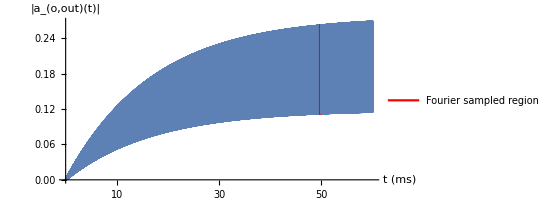

```mathematica
outAbs[t_]:=Subscript[κ, o]/(√Subscript[κ, o,ex])Abs[Subscript[a, o][t]]/.HigginPaper/.solConst;
p=OutputPiecewisePlot[outAbs,50000-1023/4,50000,60000,{2000,200,500}];
p=Show[p,AxesLabel -> {Style["t (ms)",18], Style[Row[{"|",Subscript[HoldForm[a],Row[{Style["o"],",out"}]],"(t)|"}],18]
            },Ticks->{Table[{k*10000,k*10},{k,1,6}],Automatic},AspectRatio->3/6]
```

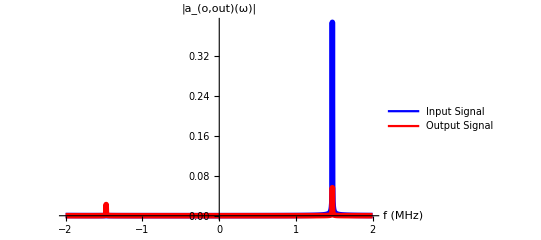

```mathematica
p=OutputFreqPlot[outputConst, 1024, 1/4, 6000,Subscript[ω, m]/.HigginPaper];
p=Show[p,AxesLabel -> {Style["f (MHz)",18], Style[Row[{"|",Subscript[HoldForm[a],Row[{Style["o"],",out"}]],"(ω)|"}],18]
            },AspectRatio->3/5]
```

In the following cells, we plot the mechanical oscillator field amplitude and its phase trajectory.

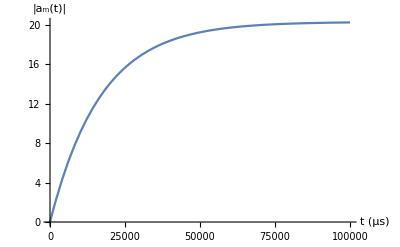

```mathematica
Plot[Evaluate[Abs[Subscript[a, m][t]]/.solConst],{t,0,tf},AxesLabel->{"t (μs)","|a_m(t)|"}]
```

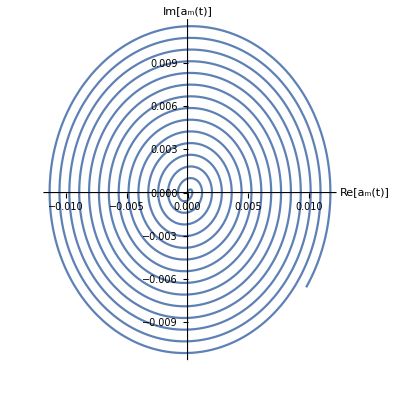

```mathematica
ParametricPlot[Evaluate[{Re[Subscript[a, m][t]],Im[Subscript[a, m][t]]}/.solConst],{t,0,10},AxesLabel->{"Re[a_m(t)]","Im[a_m(t)]"}]
```

### Oscillating drive

#### Sanity check

```mathematica
Amat//MatrixForm
```

(-ⅈ Δ_o-κ_o/2 | 0 | -ⅈ G_o | 0 | 0 | -ⅈ G_o
0 | -ⅈ Δ_e-κ_e/2 | -ⅈ G_e | 0 | 0 | -ⅈ G_e
-ⅈ Conjugate[G_o] | -ⅈ Conjugate[G_e] | -κ_m/2-ⅈ ω_m | -ⅈ G_o | -ⅈ G_e | 0
0 | 0 | ⅈ Conjugate[G_o] | ⅈ Δ_o-κ_o/2 | 0 | ⅈ Conjugate[G_o]
0 | 0 | ⅈ Conjugate[G_e] | 0 | ⅈ Δ_e-κ_e/2 | ⅈ Conjugate[G_e]
ⅈ Conjugate[G_o] | ⅈ Conjugate[G_e] | 0 | ⅈ G_o | ⅈ G_e | -κ_m/2+ⅈ ω_m)

Because the steady state solution of G_i is an oscillating function of the form  G_i=A_i e^(±ⅈω_dt), we can split the A matrix into three parts: A(t)=A_d+A_-*ⅇ^-iω_dt+A_+*ⅇ^(iω_d t).

```mathematica
Ad//MatrixForm
```

(-ⅈ Δ_o-κ_o/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ Δ_e-κ_e/2 | 0 | 0 | 0 | 0
0 | 0 | -κ_m/2-ⅈ ω_m | 0 | 0 | 0
0 | 0 | 0 | ⅈ Δ_o-κ_o/2 | 0 | 0
0 | 0 | 0 | 0 | ⅈ Δ_e-κ_e/2 | 0
0 | 0 | 0 | 0 | 0 | -κ_m/2+ⅈ ω_m)

```mathematica
Am//MatrixForm
```

(0 | 0 | -ⅈ G_o | 0 | 0 | -ⅈ G_o
0 | 0 | -ⅈ G_e | 0 | 0 | -ⅈ G_e
0 | 0 | 0 | -ⅈ G_o | -ⅈ G_e | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ G_o | ⅈ G_e | 0)

```mathematica
Ap//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
-ⅈ Conjugate[G_o] | -ⅈ Conjugate[G_e] | 0 | 0 | 0 | 0
0 | 0 | ⅈ Conjugate[G_o] | 0 | 0 | ⅈ Conjugate[G_o]
0 | 0 | ⅈ Conjugate[G_e] | 0 | 0 | ⅈ Conjugate[G_e]
ⅈ Conjugate[G_o] | ⅈ Conjugate[G_e] | 0 | 0 | 0 | 0)

#### Transfer function

```mathematica
transFOsc=SolveTransferOsc[Ad,Ap,Am,1,Subscript[ω, m],Subscript[ω, m]];
```

```mathematica
transFOsc[[1,2]]/.{Subscript[Δ, o]->Subscript[ω, m],Subscript[Δ, e]->Subscript[ω, m]}
```

(32 ⅈ G_o √(κ_(e,ex)) κ_o ω_m Conjugate[G_e])/(√(κ_(o,ex)) (-16 ⅈ G_e κ_o ω_m Conjugate[G_e]+κ_e (κ_m κ_o (κ_m+4 ⅈ ω_m)-16 ⅈ G_o ω_m Conjugate[G_o])))

```mathematica
(*Transduction efficiency Subscript[η, os] under the symmetric assumption*)
etaOsc=FullSimplify[transFOsc[[1,2]]/.{Subscript[Δ, e]->Subscript[ω, m],Subscript[Δ, o]->Subscript[ω, m],ω->Subscript[ω, m]}/.{Subscript[G, o]->Subscript[g, o]*SolveSteadyOsc[Subscript[ω, m],Subscript[κ, o],Subscript[Ω, o],2*Subscript[ω, m]],Subscript[G, e]->Subscript[g, e]*SolveSteadyOsc[Subscript[ω, m],Subscript[κ, e],Subscript[Ω, e],2*Subscript[ω, m]]},Assumptions->AssumptionRealValues]
```

-(128 g_e g_o √(κ_(e,ex)) κ_o (κ_e-2 ⅈ ω_m) (κ_o+2 ⅈ ω_m) ω_m Ω_e Ω_o)/(√(κ_(o,ex)) (64 g_e^2 κ_o ω_m (κ_o^2+4 ω_m^2) Ω_e^2+κ_e (κ_e^2+4 ω_m^2) (ⅈ κ_m κ_o (κ_m+4 ⅈ ω_m) (κ_o^2+4 ω_m^2)+64 g_o^2 ω_m Ω_o^2)))

```mathematica
ηON=Abs[transFOsc[[1,2]]]/.{Subscript[G, o]->Subscript[g, o]*SolveSteadyOsc[Subscript[ω, m],Subscript[κ, o],Subscript[Ω, o],2*Subscript[ω, m]],Subscript[G, e]->Subscript[g, e]*SolveSteadyOsc[Subscript[ω, m],Subscript[κ, e],Subscript[Ω, e],2*Subscript[ω, m]]}/.HigginPaper
```

1.83731

```mathematica
FullSimplify[etaOsc/etaConst,Assumptions->AssumptionRealValues]
```

((κ_e-2 ⅈ ω_m)^2 (κ_o+2 ⅈ ω_m)^2 (-(256 g_e κ_o (κ_o-4 ⅈ ω_m) ω_m^2 Conjugate[g_e] Ω_e^2)/(κ_e^2+4 ω_m^2)+κ_e (κ_e-4 ⅈ ω_m) (κ_m κ_o (κ_m-4 ⅈ ω_m) (κ_o-4 ⅈ ω_m)-(256 g_o ω_m^2 Conjugate[g_o] Ω_o^2)/(κ_o^2+4 ω_m^2))))/((κ_e-4 ⅈ ω_m) (ⅈ κ_o+4 ω_m) (-64 g_e κ_o ω_m (κ_o^2+4 ω_m^2) Conjugate[g_e] Ω_e^2+κ_e (κ_e^2+4 ω_m^2) (κ_m κ_o (-ⅈ κ_m+4 ω_m) (κ_o^2+4 ω_m^2)-64 g_o ω_m Conjugate[g_o] Ω_o^2)))

Calculate the efficiency gain in the limit of κ_m->0

```mathematica
Simplify[etaOsc/etaConst/.{Subscript[κ, m]->0,Subscript[g, e]->g,Subscript[g, o]->g,Subscript[Ω, e]->Ω,Subscript[Ω, o]->Ω,Subscript[κ, e]->κ,Subscript[κ, o]->κ},Assumptions->AssumptionRealValues]
```

-(4 ⅈ ω_m)/(κ-4 ⅈ ω_m)

```mathematica
symEtaRatio=FullSimplify[etaOsc/etaConst/.{Subscript[g, o]->g,Subscript[g, e]->g,Subscript[κ, o]->κ,Subscript[κ, e]->κ,Subscript[Ω, e]->Ω,Subscript[Ω, o]->Ω},Assumptions->AssumptionRealValues];
symEtaRN=symEtaRatio/.{κ->2.5*2*π,g->3.8*2*π*10^-6,Subscript[ω, m]->1.4732*2*π,Ω->2*π*500}//Simplify
```

((0.000258847+0.000610134 ⅈ)-(2.30221×10^-15-37.0256 ⅈ) κ_m-(1.+0. ⅈ) κ_m^2)/((0.+0.000719949 ⅈ)-(0.+37.0256 ⅈ) κ_m-(1.+0. ⅈ) κ_m^2)

Calculate efficiency gain in the limit of κ_m->∞

```mathematica
Limit[symEtaRatio,Subscript[κ, m]->Infinity]
```

1

The numerator of the efficiency gain:

```mathematica
Collect[Numerator[symEtaRatio],Subscript[κ, m]]
```

512 ⅈ g^2 Ω^2 ω_m^2+κ_m^2 (-ⅈ κ^4-4 κ^3 ω_m-4 ⅈ κ^2 ω_m^2-16 κ ω_m^3)+κ_m (-4 κ^4 ω_m+16 ⅈ κ^3 ω_m^2-16 κ^2 ω_m^3+64 ⅈ κ ω_m^4)

The denominator of the efficiency gain :

```mathematica
Collect[Denominator[symEtaRatio],Subscript[κ, m]]
```

-128 g^2 Ω^2 (κ-4 ⅈ ω_m) ω_m+κ_m^2 (κ-4 ⅈ ω_m) (-ⅈ κ^3-4 ⅈ κ ω_m^2)+κ_m (κ-4 ⅈ ω_m) (4 κ^3 ω_m+16 κ ω_m^3)

Note they are both 2nd order polynomials with the same coefficient before κ_m^2.

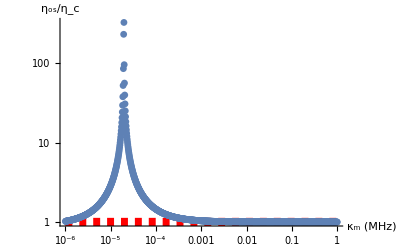

```mathematica
p1=ListLogLogPlot[Table[{x,Abs[symEtaRN/.{Subscript[κ, m]->x}]},{x,Logspace[-6,0,1000]}],PlotRange->All,PlotMarkers->{Automatic,Small},BaseStyle->{FontFamily -> "Times New Roman", 15}, LabelStyle -> {FontFamily -> 
            "Times New Roman"},AxesLabel->{Style[Row[{Subscript[κ,Style["m"]]," (MHz)"}]], Style[Row[{Subscript[η,"os"],"/",Subscript[η,"c"]}]]}];
p2=LogLogPlot[1,{x,10^-6,1},PlotStyle->{Red,Dashed,Thickness[0.015]}];
pη=Show[{p1,p2},PlotRange->All]
```

#### Numerical simulation

```mathematica
(*Solve the system dynamics for a total evolution time of tf*)
tf=100000;
solOsc=SolveTransducerOscDrive[HigginPaper,tf];
outputOsc[t_]:=Subscript[κ, o]/(√Subscript[κ, o,ex])Subscript[a, o][t]/.HigginPaper/.solOsc;
```

## Visualization

### Cavity light field amplitudes

Here we plot the cavity light field amplitudes.

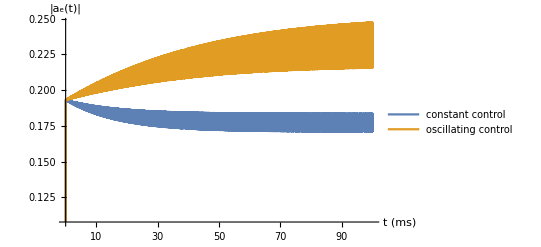

```mathematica
p=Plot[{Evaluate[Abs[Subscript[a, e][t]]/.solConst],Evaluate[Abs[Subscript[a, e][t]]/.solOsc]},{t,0,tf},AxesLabel->{"t (ms)",Row[{"|",Subscript[a,Style["e"]],"(t)|"}]},Ticks->{Table[{k*10000,k*10},{k,1,10}],Automatic},BaseStyle->{FontFamily->"Times New Roman",15},LabelStyle->{FontFamily->"Times New Roman"},PlotPoints->400,PlotLegends->Placed[{"constant control", "oscillating control"},{0.7,0.2}]]
```

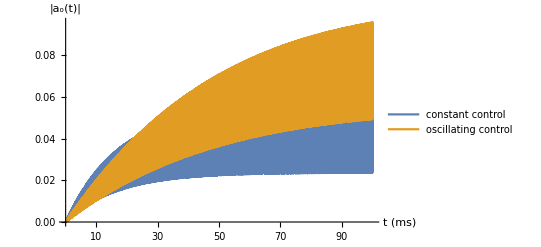

```mathematica
p=Plot[{Evaluate[Abs[Subscript[a, o][t]]/.solConst],Evaluate[Abs[Subscript[a, o][t]]/.solOsc]},{t,0,tf},AxesLabel->{"t (ms)",Row[{"|",Subscript[a,Style["o"]],"(t)|"}]},Ticks->{Table[{k*10000,k*10},{k,1,10}],Automatic},BaseStyle->{FontFamily->"Times New Roman",15},LabelStyle->{FontFamily->"Times New Roman"},PlotPoints->400,PlotLegends->Placed[{"constant control", "oscillating control"},{0.3,0.85}]]
```

### Mechanical oscillator field amplitude and phase space trajectory

Here we plot the mechanical oscillator field amplitude and its phase space trajectory.

```mathematica
pm=ParametricPlot[Evaluate[{Re[Subscript[a, m][t]],Im[Subscript[a, m][t]]}/.solOsc],{t,0,5},AxesLabel->{Style[Row[{"Re[",Subscript[a,Style["m"]],"(t)]"}]],Style[Row[{"Im[",Subscript[a,Style["m"]],"(t)]"}]]},PlotPoints->1000,BaseStyle ->
             {FontFamily -> "Times New Roman",6},Ticks->None,Frame->True,FrameTicks->None,PlotStyle->Red]
p1=ListPlot[Table[{t,Abs[Subscript[a, m][t]]/.solConst[[1]]},{t,Subdivide[1000,100000,1000]}],AxesLabel->{"t (ms)",Style[Row[{"|",Subscript[a,Style["m"]],"(t)|"}]]},PlotRange->All,Ticks->{Table[{k*10000,k*10},{k,1,10}],Automatic},BaseStyle->{FontFamily->"Times New Roman",15},LabelStyle->{FontFamily->"Times New Roman"},PlotStyle->Blue,PlotMarkers->{Automatic,Tiny}];
p2=ListPlot[Table[{t,Abs[Subscript[a, m][t]]/.solOsc[[1]]},{t,Subdivide[1000,100000,1000]}],PlotStyle->Red,PlotMarkers->{Automatic,Tiny}];
p=Show[{p1,p2},Epilog->Inset[pm,{16000,40},{0,0},{35000,Automatic}],PlotRange->All];
p=Legended[p,Placed[PointLegend[{Blue}, {Style["Constant control",
             FontFamily -> "Times New Roman", 15]}], {0.3,1.0}]]
```

-Graphics-

### Transduction efficiency

Here we plot the transduction efficiency.

```mathematica
xAxis=Subdivide[1000,100000,1000];
ηC=GetEfficiency[outputConst,1024,1/4,Subscript[ω, m]/.HigginPaper,xAxis];
ηO=GetEfficiency[outputOsc,1024,1/4,Subscript[ω, m]/.HigginPaper,xAxis];
```

```mathematica
p1=ListPlot[{Transpose[{xAxis,ηC}],Transpose[{xAxis,ηO}]},PlotStyle->{Blue,Red},BaseStyle->{FontFamily -> "Times New Roman", 15},PlotMarkers->{Automatic,Tiny},Ticks->{Table[{k*10000,k*10},{k,1,10}],Automatic},LabelStyle -> {FontFamily -> 
            "Times New Roman"},AxesLabel->{"t (ms)", Style[Row[{"η(",Subscript[ω,Style["m"]],")"}]]}];
p2=Plot[ηCN,{t,0,100000},PlotStyle->{Blue,Dashed}];
p=Show[{p1,p2},PlotRange->All];
p=Legended[p,Placed[PointLegend[{Red}, {Style["Oscillating control",
             FontFamily -> "Times New Roman", 15]}], {0.7,1.0}]]
```

-Graphics-